Using MagneticTB 1.0

MagneticTB 2.0 includes the functions from version 1.0. To continue using a 1.0 notebook, load MagneticTBOld` and use the function names ending in old. The graphene example below shows how to initialize a model, calculate its Hamiltonian, and plot the bands with these functions.

Load MagneticTB 1.0

Start a fresh kernel and load MagneticTBOld` with the following command. Use separate kernels for versions 1.0 and 2.0:

```mathematica
Needs["MagneticTBOld`"]
```

Initialize the model with version 1.0

For graphene, give the hexagonal lattice, one representative carbon position, and its pz orbital. The symmetry operations generate the second carbon atom. In version 1.0, the function and option names below all end in old:

```mathematica
grapheneOperationsOld = msgopold[grayold[191]];
initold[
  latticeold -> {
    {aold, 0, 0},
    {-aold/2, Sqrt[3] aold/2, 0},
    {0, 0, cold}
  },
  lattparold -> {aold -> 1, cold -> 3},
  wyckoffpositionold -> {
    {{1/3, 2/3, 0}, {0, 0, 0}}
  },
  symminformationold -> grapheneOperationsOld,
  basisFunctionsold -> {{"pz"}},
  debugQold -> False
];
```

Construct and display the Hamiltonian with version 1.0

```mathematica
hOldOnsite = symhamold[1];
hOldNearest = symhamold[2];
hOld = hOldOnsite + hOldNearest;
MatrixForm[hOld]
```

(e1old | ⅇ^(ⅈ (-(2 kxold)/3-kyold/3)) t1old+ⅇ^(ⅈ (kxold/3-kyold/3)) t1old+ⅇ^(ⅈ (kxold/3+(2 kyold)/3)) t1old
ⅇ^(ⅈ (-kxold/3-(2 kyold)/3)) t1old+ⅇ^(ⅈ (-kxold/3+kyold/3)) t1old+ⅇ^(ⅈ ((2 kxold)/3+kyold/3)) t1old | e1old)

Plot the bands with version 1.0

```mathematica
oldPath = {
  {{{0, 0, 0}, {0, 1/2, 0}}, {"G", "M"}},
  {{{0, 1/2, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "G"}}
};
bandManipulateold[oldPath, 30, hOld]
```

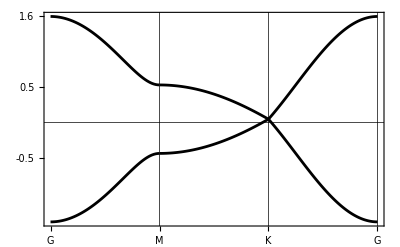

```mathematica
bandplotold[
  oldPath,
  60,
  hOld,
  {e1old -> 0.05, t1old -> 0.5}
]
```

Compare results from versions 1.0 and 2.0

To compare versions 1.0 and 2.0, enter the same lattice, positions, symmetry, and orbitals in two separate kernels. Then compare the Hamiltonians and bands. Each version needs its own initialization; neither uses the model set up in the other kernel.

Related functions

initold ▪ symhamold ▪ bandManipulateold ▪ MagneticTB

History